## Tutorial-Examples for xBrauer

## I. Loading package

```mathematica
<<xAct`xBrauer`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

Package xAct`TraceFree`  version 0.1.0, {2013,11,12}

Copyright (C) 2013, Leo C. Stein, under the General Public License.

------------------------------------------------------------

Package xAct`xBrauer`  version 0.0.2, {2021,11,9}

Copyright (C) 2020, Thomas Helpin, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## II. Basics of the Brauer algebra

This packages is mainly based on the following mathematical literature on the Brauer Algebra,

R.Brauer “On Algebras Which are Connected with the Semisimple Continuous Groups”  : Annals of Mathematics Second Series, Vol. 38, No. 4 (Oct., 1937), pp. 857-872 
Wm. P. Brown “An algebra related to the orthogonal group.,” Michigan Mathematical Journal, Michigan Math. J. 3(1), 1-22, (1955/1956) 
H.Wenzl  “On the structure of Brauer’s centralizer algebras “ : Annals of Mathematics Second Series, Vol. 128, No. 1 (Jul., 1988), pp. 173-193
 Arun Ram “Characters of Brauer’s centralizer algebras.,” Pacific Journal of Mathematics, Pacific J. Math. 169(1), 173-200, (1995)
Shalile, A. “On the Center of the Brauer Algebra”. Algebr Represent Theor 16, 65–100 (2013). https://doi.org/10.1007/s10468-011-9294-2
O.King, P.Martin, and A.Parker “ On central idempotents in the Brauer algebra “ : Journal of Algebra 512, 20 (2018) 

... and on the following literature on Weingarten Calculus :

Collins, B., Śniady, P. Integration with Respect to the Haar Measure on Unitary, Orthogonal and Symplectic Group. Commun. Math. Phys. 264, 773–795 (2006). https://doi.org/10.1007/s00220-006-1554-3
Collins, B., Matsumoto, S.     On some properties of orthogonal Weingarten functions  J. Math. Phys. 50, 113516 (2009); https://doi.org/10.1063/1.3251304

I am very grateful to Yegor Goncharov who introduced me to the Brauer Algebra. This packages was developed during a year of conjoint research on the Brauer algebra with Yegor Goncharov, without  whom this packages would certainly not exist.

### 1. Elements of the Brauer monoïd

The elements of the Brauer monoïd Br(n) are perfect matchings among the 2n elements {1,2,..n}U{n+1,n+2,...,2n}

```mathematica
?BrauerList
```

```mathematica
?BrauerElements
```

```mathematica
BrauerElements[2]
```

{{{1,2},{3,4}}_B,{{1,3},{2,4}}_B,{{1,4},{2,3}}_B}

```mathematica
BrauerElements[3]
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

### 2. Diagrammatic output

The Brauer elements can be represented in the form of diagrams :

```mathematica
?BrauerGraph
```

```mathematica
?BrauerDiagram
```

```mathematica
Options@BrauerDiagram
```

{VertexSize→Tiny,ImageSize→Tiny,EdgeStyle→Automatic}

```mathematica
BrauerElements[3]
BrauerDiagram[#,ImageSize->60]&/@%
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

Elements with no arcs are elements of the symmetric group.

```mathematica
?SymmetricGroupQ
```

```mathematica
BrauerElements[3]
BrauerDiagram[#,ImageSize->60]&/@%
SymmetricGroupQ[ToBrauerList[#]]&/@%
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{False,False,False,False,False,False,False,True,True,False,True,True,False,True,True}

### 3. Product in the Brauer monoïd

The Brauer product between two diagrams d1 and d2 is performed by following the path of the edges when merging the two diagrams. If the edges form a loop the resulting diagram picks a additional factor dtrace.

```mathematica
?BrauerProduct
```

```mathematica
?dtrace
```

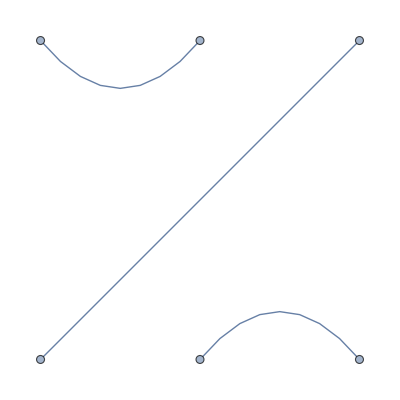
-Graphics-_B_g

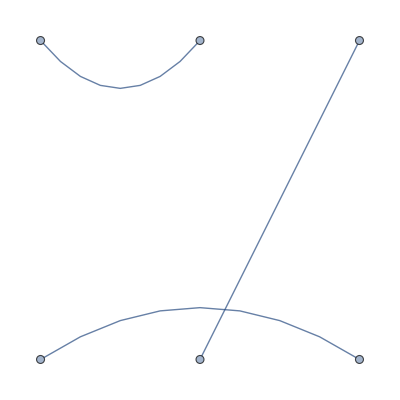
-Graphics-_B_g

-Graphics-_B_g

```mathematica
BrauerDiagram@BrauerElements[3][[1]]
BrauerDiagram@BrauerElements[3][[2]]
BrauerDiagram@BrauerProduct[%,%%]
```

When  two arcs close (forming a loop), the resulting diagram picks of factor dtrace :

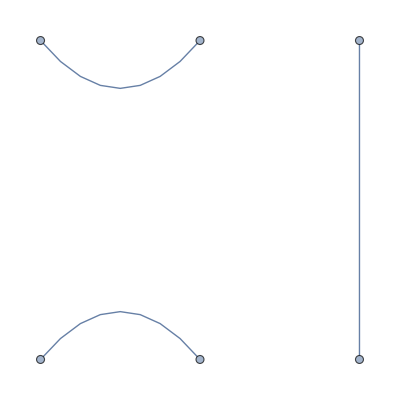
-Graphics-_B_g

-Graphics-_B_g

d -Graphics-_B_g

```mathematica
BrauerDiagram@BrauerElements[3][[3]]
BrauerDiagram@BrauerElements[3][[1]]
BrauerDiagram@BrauerProduct[%,%%]
```

```mathematica
BrauerElements[3]
BrauerDiagram[#,ImageSize->20]&/@Flatten[Outer[BrauerProduct,%,%]]
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

{(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,d (-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

### 4. “Generating set” for the Brauer monoïd

```mathematica
?BrauerGenerators
```

```mathematica
Options@BrauerGenerators
```

{StrongGenSet→True}

{{{1,5},{2,4},{3,6}}_B,{{1,6},{2,4},{3,5}}_B,{{1,2},{3,6},{4,5}}_B}

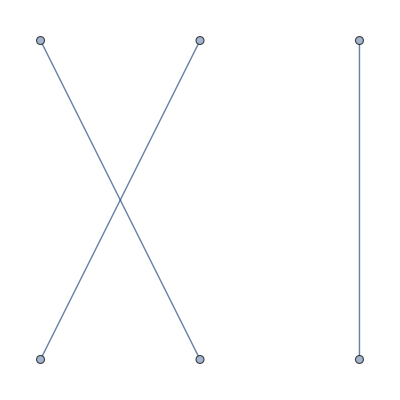
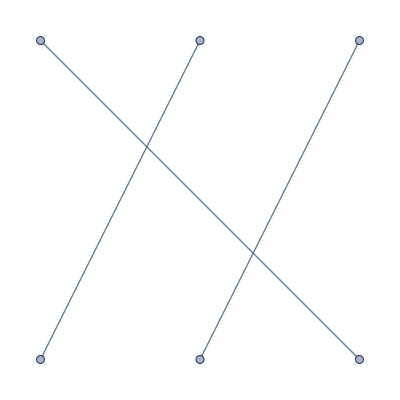
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

```mathematica
BrauerGenerators[3]
BrauerDiagram/@%
```

{{{1,6},{2,5},{3,7},{4,8}}_B,{{1,8},{2,5},{3,6},{4,7}}_B,{{1,2},{3,7},{4,8},{5,6}}_B}

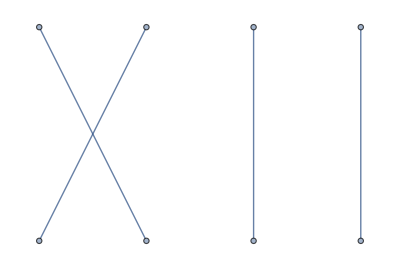
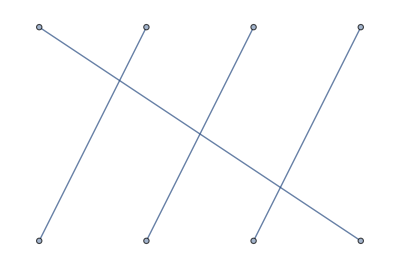
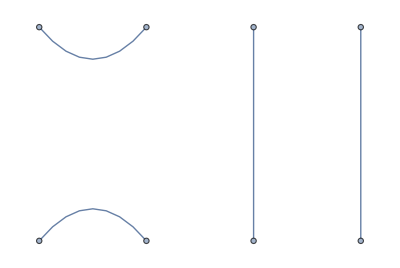
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

```mathematica
BrauerGenerators[4]
BrauerDiagram/@%
```

{{{1,6},{2,5},{3,7},{4,8}}_B,{{1,5},{2,7},{3,6},{4,8}}_B,{{1,5},{2,6},{3,8},{4,7}}_B,{{1,2},{3,7},{4,8},{5,6}}_B,{{1,5},{2,3},{4,8},{6,7}}_B,{{1,5},{2,6},{3,4},{7,8}}_B}

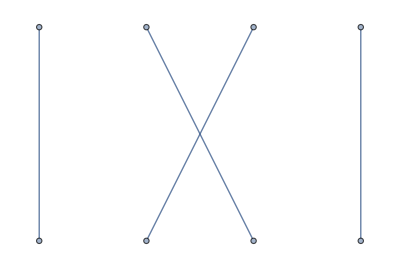
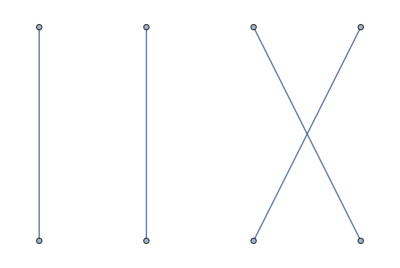
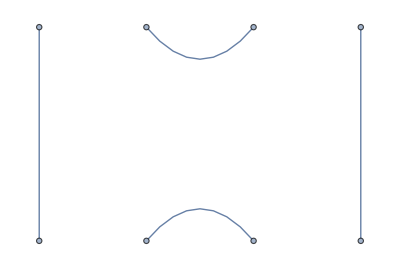
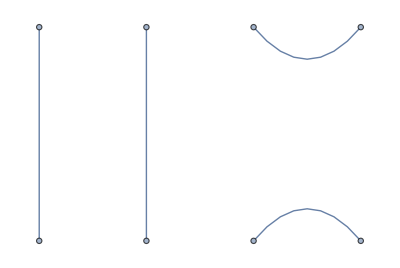
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

```mathematica
BrauerGenerators[4,StrongGenSet->False]
BrauerDiagram/@%
```

{{{1,7},{2,6},{3,8},{4,9},{5,10}}_B,{{1,6},{2,8},{3,7},{4,9},{5,10}}_B,{{1,6},{2,7},{3,9},{4,8},{5,10}}_B,{{1,6},{2,7},{3,8},{4,10},{5,9}}_B,{{1,2},{3,8},{4,9},{5,10},{6,7}}_B,{{1,6},{2,3},{4,9},{5,10},{7,8}}_B,{{1,6},{2,7},{3,4},{5,10},{8,9}}_B,{{1,6},{2,7},{3,8},{4,5},{9,10}}_B}

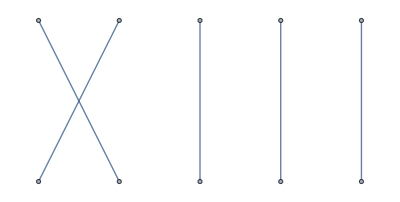
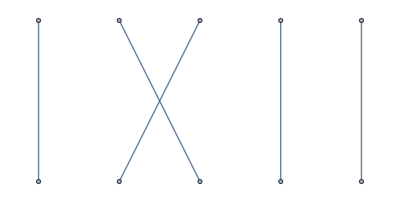
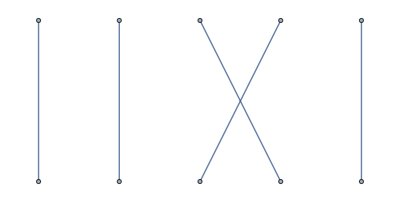
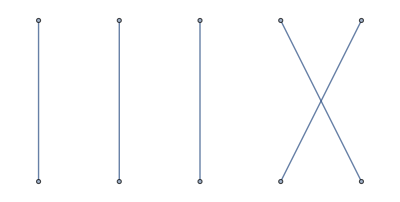
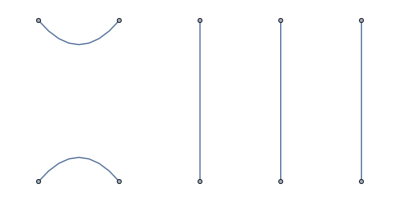
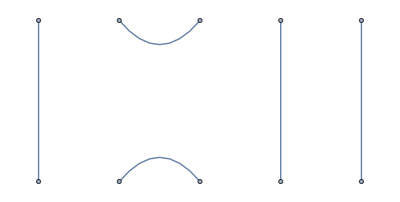
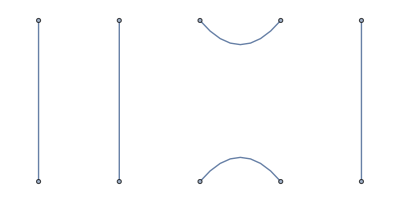
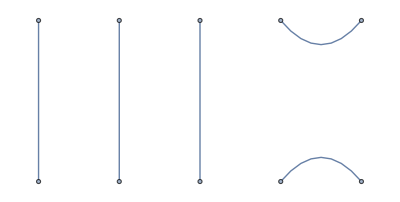
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

```mathematica
BrauerGenerators[5,StrongGenSet->False]
BrauerDiagram/@%
```

### 5. Brauer Algebra

One can write linear combinations of the elements of the Brauer monoïd to form the Brauer Algebra

```mathematica
BrauerElements[3]
Plus@@%
BrauerProduct[%,%]
BrauerDiagram[#,ImageSize->40]&/@%
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

{{1,2},{3,4},{5,6}}_B+{{1,2},{3,5},{4,6}}_B+{{1,2},{3,6},{4,5}}_B+{{1,3},{2,4},{5,6}}_B+{{1,3},{2,5},{4,6}}_B+{{1,3},{2,6},{4,5}}_B+{{1,4},{2,3},{5,6}}_B+{{1,4},{2,5},{3,6}}_B+{{1,4},{2,6},{3,5}}_B+{{1,5},{2,3},{4,6}}_B+{{1,5},{2,4},{3,6}}_B+{{1,5},{2,6},{3,4}}_B+{{1,6},{2,3},{4,5}}_B+{{1,6},{2,4},{3,5}}_B+{{1,6},{2,5},{3,4}}_B

18 {{1,2},{3,4},{5,6}}_B+3 d {{1,2},{3,4},{5,6}}_B+18 {{1,2},{3,5},{4,6}}_B+3 d {{1,2},{3,5},{4,6}}_B+18 {{1,2},{3,6},{4,5}}_B+3 d {{1,2},{3,6},{4,5}}_B+18 {{1,3},{2,4},{5,6}}_B+3 d {{1,3},{2,4},{5,6}}_B+18 {{1,3},{2,5},{4,6}}_B+3 d {{1,3},{2,5},{4,6}}_B+18 {{1,3},{2,6},{4,5}}_B+3 d {{1,3},{2,6},{4,5}}_B+18 {{1,4},{2,3},{5,6}}_B+3 d {{1,4},{2,3},{5,6}}_B+6 {{1,4},{2,5},{3,6}}_B+6 {{1,4},{2,6},{3,5}}_B+18 {{1,5},{2,3},{4,6}}_B+3 d {{1,5},{2,3},{4,6}}_B+6 {{1,5},{2,4},{3,6}}_B+6 {{1,5},{2,6},{3,4}}_B+18 {{1,6},{2,3},{4,5}}_B+3 d {{1,6},{2,3},{4,5}}_B+6 {{1,6},{2,4},{3,5}}_B+6 {{1,6},{2,5},{3,4}}_B

18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+6 (-Graphics-)_B_g+6 (-Graphics-)_B_g+6 (-Graphics-)_B_g+6 (-Graphics-)_B_g+6 (-Graphics-)_B_g+6 (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g+18 (-Graphics-)_B_g+3 d (-Graphics-)_B_g

### 6. Jucys-Murphy elements (no applications implemented yet )

```mathematica
?JucysMurphy
```

```mathematica
Options@JucysMurphy
```

{SymmetricGroupOnly→False}

Jucys Murphy for the symmetric group

```mathematica
JucysMurphy[4,SymmetricGroupOnly->True]
BrauerDiagram[#,ImageSize->40]&/@%
```

{0,{{1,6},{2,5},{3,7},{4,8}}_B,{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B,{{1,5},{2,6},{3,8},{4,7}}_B+{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B}

{0,(-Graphics-)_B_g,(-Graphics-)_B_g+(-Graphics-)_B_g,(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g}

```mathematica
(** Cycle notation **)
```

```mathematica
?BrauerToPerm
Options@BrauerToPerm
```

{PermNotation→Perm}

```mathematica
JucysMurphy[4,SymmetricGroupOnly->True]
BrauerToPerm[#,PermNotation->Cycles]&/@%
```

{0,{{1,6},{2,5},{3,7},{4,8}}_B,{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B,{{1,5},{2,6},{3,8},{4,7}}_B+{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B}

{0,(2,1),(2,1)+(3,2),(2,1)+(3,2)+(4,3)}

Jucys-Murphy elements for the Brauer Algebra

```mathematica
JucysMurphy[3]
BrauerDiagram[#,ImageSize->40]&/@%
```

{0,-{{1,2},{3,6},{4,5}}_B+{{1,5},{2,4},{3,6}}_B,-{{1,3},{2,5},{4,6}}_B-{{1,4},{2,3},{5,6}}_B+{{1,4},{2,6},{3,5}}_B+{{1,5},{2,4},{3,6}}_B}

{0,-(-Graphics-)_B_g+(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g}

```mathematica
JucysMurphy[4]
BrauerDiagram[#,ImageSize->40]&/@%
```

{0,-{{1,2},{3,7},{4,8},{5,6}}_B+{{1,6},{2,5},{3,7},{4,8}}_B,-{{1,3},{2,6},{4,8},{5,7}}_B-{{1,5},{2,3},{4,8},{6,7}}_B+{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B,-{{1,4},{2,6},{3,7},{5,8}}_B-{{1,5},{2,4},{3,7},{6,8}}_B-{{1,5},{2,6},{3,4},{7,8}}_B+{{1,5},{2,6},{3,8},{4,7}}_B+{{1,5},{2,7},{3,6},{4,8}}_B+{{1,6},{2,5},{3,7},{4,8}}_B}

{0,-(-Graphics-)_B_g+(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g-(-Graphics-)_B_g}

```mathematica
JucysMurphy[5]
BrauerDiagram[#,ImageSize->40]&/@%
```

{0,-{{1,2},{3,8},{4,9},{5,10},{6,7}}_B+{{1,7},{2,6},{3,8},{4,9},{5,10}}_B,-{{1,3},{2,7},{4,9},{5,10},{6,8}}_B-{{1,6},{2,3},{4,9},{5,10},{7,8}}_B+{{1,6},{2,8},{3,7},{4,9},{5,10}}_B+{{1,7},{2,6},{3,8},{4,9},{5,10}}_B,-{{1,4},{2,7},{3,8},{5,10},{6,9}}_B-{{1,6},{2,4},{3,8},{5,10},{7,9}}_B-{{1,6},{2,7},{3,4},{5,10},{8,9}}_B+{{1,6},{2,7},{3,9},{4,8},{5,10}}_B+{{1,6},{2,8},{3,7},{4,9},{5,10}}_B+{{1,7},{2,6},{3,8},{4,9},{5,10}}_B,-{{1,5},{2,7},{3,8},{4,9},{6,10}}_B-{{1,6},{2,5},{3,8},{4,9},{7,10}}_B-{{1,6},{2,7},{3,5},{4,9},{8,10}}_B-{{1,6},{2,7},{3,8},{4,5},{9,10}}_B+{{1,6},{2,7},{3,8},{4,10},{5,9}}_B+{{1,6},{2,7},{3,9},{4,8},{5,10}}_B+{{1,6},{2,8},{3,7},{4,9},{5,10}}_B+{{1,7},{2,6},{3,8},{4,9},{5,10}}_B}

{0,-(-Graphics-)_B_g+(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g-(-Graphics-)_B_g,-(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g+(-Graphics-)_B_g-(-Graphics-)_B_g-(-Graphics-)_B_g-(-Graphics-)_B_g}

## III. Conjugacy Classes

### 1. Non Standard Young Tableau representation of the conjugacy classes :

```mathematica
?BrauerTab
```

```mathematica
?BrauerTableaux
```

```mathematica
BrauerTableaux[2]
TableauForm/@Flatten@%
```

{{{{1,2}}_Tab}}

{1 | 2}

```mathematica
BrauerTableaux[3]
TableauForm/@Flatten@%
```

{{{{1,2,3}}_Tab,{{1,2},{3}}_Tab}}

{1 | 2 | 3,1 | 2
3 | }

```mathematica
BrauerTableaux[4]
TableauForm/@Flatten@%
```

{{{{1,2,3,3}}_Tab,{{1,3,2,3}}_Tab,{{1,2,3},{3}}_Tab,{{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab},{{{1,2,1,2}}_Tab,{{1,2},{1,2}}_Tab}}

{1 | 2 | 3 | 3,1 | 3 | 2 | 3,1 | 2 | 3
3 |  | ,1 | 2
3 | 3,1 | 2
3 | 
3 | ,1 | 2 | 1 | 2,1 | 2
1 | 2}

****For each BrauerTab there is a canonical representative :

```mathematica
?BrauerTabToRep
```

{{{1,2,3,3}}_Tab,{{1,3,2,3}}_Tab,{{1,2,3},{3}}_Tab,{{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab,{{1,2,1,2}}_Tab,{{1,2},{1,2}}_Tab}

{{{1,2},{3,8},{4,5},{6,7}}_B,{{1,2},{3,6},{4,5},{7,8}}_B,{{1,2},{3,5},{4,8},{6,7}}_B,{{1,2},{3,8},{4,7},{5,6}}_B,{{1,2},{3,7},{4,8},{5,6}}_B,{{1,2},{3,4},{5,8},{6,7}}_B,{{1,2},{3,4},{5,6},{7,8}}_B}

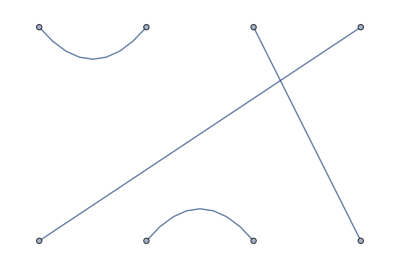
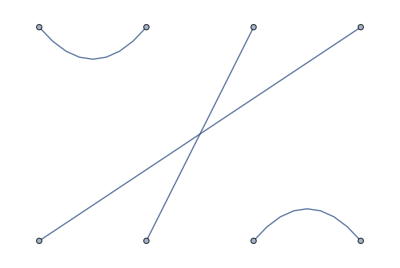
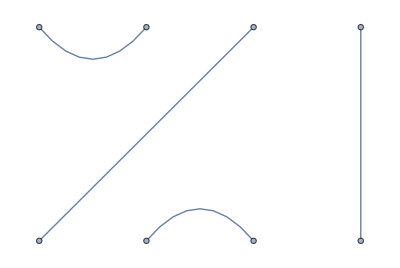
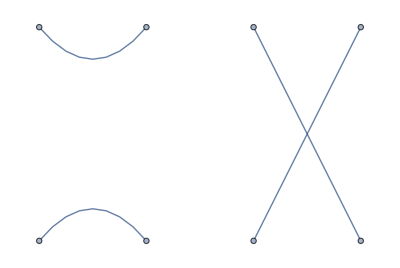
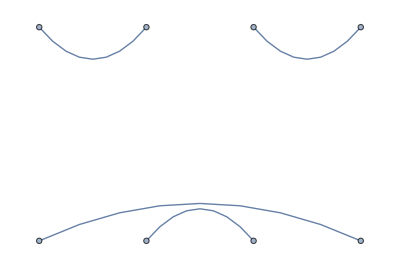
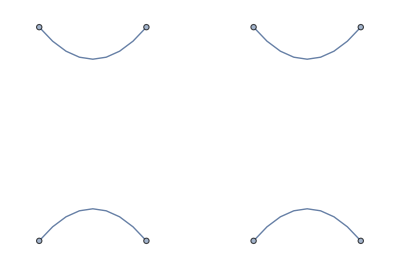
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

```mathematica
Flatten@BrauerTableaux[4]
BrauerTabToRep/@%
BrauerDiagram/@%
```

A Brauer Tableau represents a sum of “equivalent” diagrams in the Brauer Algebra

{{{1,2,3}}_Tab,{{1,2},{3}}_Tab}

{{{1,2},{3,4},{5,6}}_B+{{1,2},{3,5},{4,6}}_B+{{1,3},{2,4},{5,6}}_B+{{1,3},{2,6},{4,5}}_B+{{1,5},{2,3},{4,6}}_B+{{1,6},{2,3},{4,5}}_B,{{1,2},{3,6},{4,5}}_B+{{1,3},{2,5},{4,6}}_B+{{1,4},{2,3},{5,6}}_B}

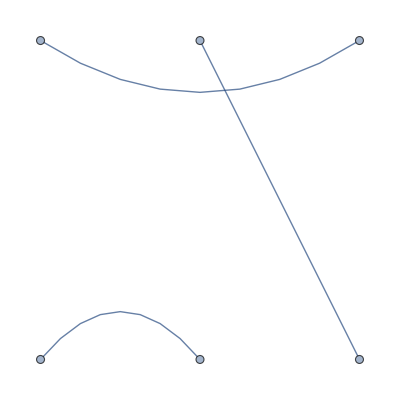
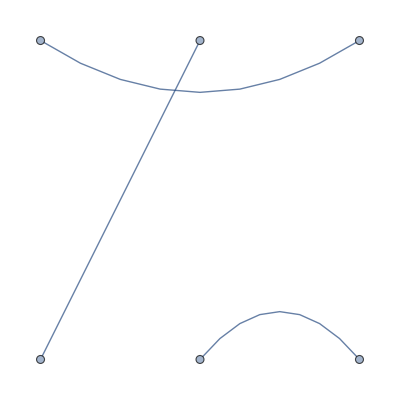
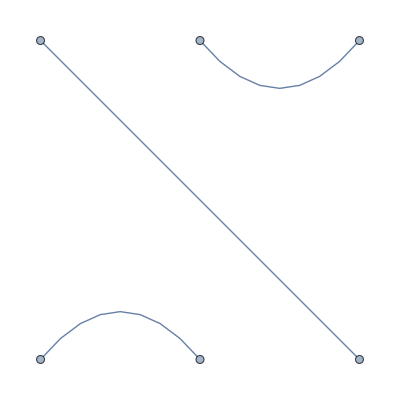
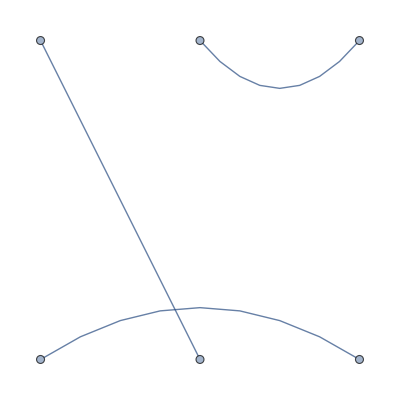
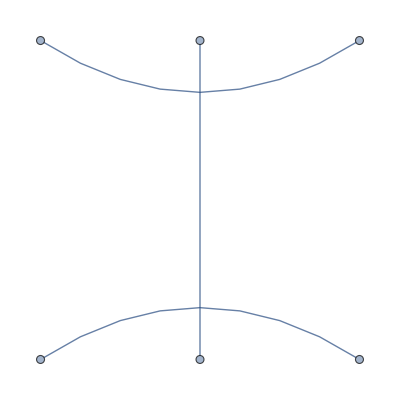
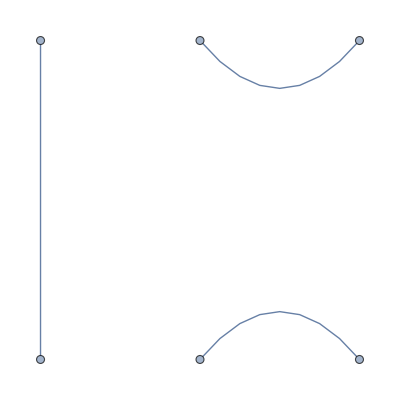
{-Graphics-_B_g+-Graphics-_B_g+-Graphics-_B_g+-Graphics-_B_g+-Graphics-_B_g+-Graphics-_B_g,-Graphics-_B_g+-Graphics-_B_g+-Graphics-_B_g}

```mathematica
Flatten@BrauerTableaux[3]
ToBrauerList/@%
BrauerDiagram/@%
```

The number of conjugacy classes in Br(n) can be computed with the algorithm of Jeb F. Willenbring : A Stable Range for Dimensions of Homogeneous
O(n)-Invariant Polynomials on the n×n Matrices - Journal of Algebra 242,691-708 (2001) ***)

```mathematica
?NumberOfBrauerTab
```

```mathematica
NumberOfBrauerTab[19]
```

187129

### 2. Algebra of Conjugacy classes

```mathematica
?ConjugacyClassRelations
```

```mathematica
Subscript[{{1,2},{3},{3}}, Tab]
ConjugacyClassRelations[%]
```

{{1,2},{3},{3}}_Tab

{{{1,2},{3},{3}}_Tab**{{1,2},{3},{3}}_Tab==2 {{1,2},{1,2}}_Tab+{{1,2,3},{3}}_Tab+d {{1,2},{3},{3}}_Tab,{{1,2},{3},{3}}_Tab**{{1,2},{3,3}}_Tab=={{1,2,3,3}}_Tab+2 {{1,2},{1,2}}_Tab+d {{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab**{{1,2,3},{3}}_Tab==4 {{1,2,1,2}}_Tab+{{1,2,3,3}}_Tab+2 {{1,3,2,3}}_Tab+(1+d) {{1,2,3},{3}}_Tab+4 {{1,2},{3},{3}}_Tab,{{1,2},{3},{3}}_Tab**{{1,3,2,3}}_Tab=={{1,2,3,3}}_Tab+d {{1,3,2,3}}_Tab+4 {{1,2},{1,2}}_Tab+{{1,2,3},{3}}_Tab,{{1,2},{3},{3}}_Tab**{{1,2,3,3}}_Tab==4 {{1,2,1,2}}_Tab+(1+d) {{1,2,3,3}}_Tab+2 {{1,3,2,3}}_Tab+4 {{1,2},{3,3}}_Tab+{{1,2,3},{3}}_Tab,{{1,2},{3},{3}}_Tab**{{1,2},{1,2}}_Tab==2 ({{1,2,1,2}}_Tab+d {{1,2},{1,2}}_Tab),{{1,2},{3},{3}}_Tab**{{1,2,1,2}}_Tab==2 (1+d) {{1,2,1,2}}_Tab+4 {{1,2},{1,2}}_Tab}

## IV. Trace/Traceless projector

The trace/traceless projector can be computed from the structure constant of the algebra of conjugacy classes in Brauer. In this program the trace/traceless projectors are expressed as a linear combination of the conjugacy classes.

```mathematica
?TracelessProjector
```

```mathematica
?TraceProjector
```

```mathematica
(*** Projectors in Br(3) ***)
```

```mathematica
TracelessProjector[3,1]
TableauForm/@%
```

({{1,2,3}}_Tab)/((-1+d) (2+d))-((1+d) {{1,2},{3}}_Tab)/((-1+d) (2+d))+{{3},{3},{3}}_Tab

(1 | 2 | 3)/((-1+d) (2+d))-((1+d) 1 | 2
3 |)/((-1+d) (2+d))+3
3
3

P^2=P :

```mathematica
ConjugacyClassProduct[TracelessProjector[3,1],TracelessProjector[3,1]];
Collect[%,Flatten@BrauerTableaux[3],Factor]
```

({{1,2,3}}_Tab)/((-1+d) (2+d))-((1+d) {{1,2},{3}}_Tab)/((-1+d) (2+d))+{{3},{3},{3}}_Tab

```mathematica
BrauerTableaux[3]
```

{{{{1,2,3}}_Tab,{{1,2},{3}}_Tab}}

```mathematica
ConjugacyClassProduct[TracelessProjector[3,1],Subscript[{{1,2},{3}}, Tab]]//Simplify
```

0

```mathematica
(*** Projectors in Br(4) ***)
```

```mathematica
TracelessProjector[4,1]
```

-((2+3 d) {{1,2,1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-({{1,2,3,3}}_Tab)/((-2+d) (2+d) (4+d))-(2 {{1,3,2,3}}_Tab)/((-2+d) d (4+d))+((6+3 d+d^2) {{1,2},{1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))+(4 {{1,2},{3,3}}_Tab)/((-2+d) d (2+d) (4+d))+((3+d) {{1,2,3},{3}}_Tab)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) {{1,2},{3},{3}}_Tab)/((-2+d) d (2+d) (4+d))+{{3},{3},{3},{3}}_Tab

```mathematica
ConjugacyClassProduct[TracelessProjector[4,1],TracelessProjector[4,1]];
Collect[%,Flatten@BrauerTableaux[4],Factor]
```

-((2+3 d) {{1,2,1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-({{1,2,3,3}}_Tab)/((-2+d) (2+d) (4+d))-(2 {{1,3,2,3}}_Tab)/((-2+d) d (4+d))+((6+3 d+d^2) {{1,2},{1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))+(4 {{1,2},{3,3}}_Tab)/((-2+d) d (2+d) (4+d))+((3+d) {{1,2,3},{3}}_Tab)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) {{1,2},{3},{3}}_Tab)/((-2+d) d (2+d) (4+d))+{{3},{3},{3},{3}}_Tab

```mathematica
ConjugacyClassProduct[TracelessProjector[4,1],Subscript[{{1,2},{3},{3}}, Tab]]//Simplify
```

0

```mathematica
TracelessProjector[4,1]
TracelessProjector[4,2]
TraceProjector[4,2]
```

-((2+3 d) {{1,2,1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-({{1,2,3,3}}_Tab)/((-2+d) (2+d) (4+d))-(2 {{1,3,2,3}}_Tab)/((-2+d) d (4+d))+((6+3 d+d^2) {{1,2},{1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))+(4 {{1,2},{3,3}}_Tab)/((-2+d) d (2+d) (4+d))+((3+d) {{1,2,3},{3}}_Tab)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) {{1,2},{3},{3}}_Tab)/((-2+d) d (2+d) (4+d))+{{3},{3},{3},{3}}_Tab

({{1,2,1,2}}_Tab)/((-1+d) d (2+d))+((2+3 d) {{1,2,1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))+({{1,2,3,3}}_Tab)/((-2+d) (2+d) (4+d))+(2 {{1,3,2,3}}_Tab)/((-2+d) d (4+d))-((1+d) {{1,2},{1,2}}_Tab)/((-1+d) d (2+d))-((6+3 d+d^2) {{1,2},{1,2}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-(4 {{1,2},{3,3}}_Tab)/((-2+d) d (2+d) (4+d))-((3+d) {{1,2,3},{3}}_Tab)/((-2+d) (2+d) (4+d))+((-4+4 d^2+d^3) {{1,2},{3},{3}}_Tab)/((-2+d) d (2+d) (4+d))

-({{1,2,1,2}}_Tab)/((-1+d) d (2+d))+((1+d) {{1,2},{1,2}}_Tab)/((-1+d) d (2+d))

```mathematica
(*** Projectors in Br(5) ***)
```

```mathematica
TracelessProjector[5,1]
TracelessProjector[5,2]
TraceProjector[5,2]
```

((6+5 d) {{1,2,1,2,3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+(d (-4-4 d+d^2) {{1,2,3,3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+((-12+2 d+3 d^2) {{1,3,2,3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))-((18+5 d+d^2) {{1,2,3},{1,2}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-(4 (-12+2 d+3 d^2) {{1,2,3},{3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(6 (-4-4 d+d^2) {{3,3,3},{1,2}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-((-18+11 d+3 d^2) {{1,2,1,2},{3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-((24-4 d-10 d^2+3 d^3+d^4) {{1,2,3,3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(2 d (-11+3 d+d^2) {{1,3,2,3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))+((-6+3 d+6 d^2+d^3) {{1,2},{1,2},{3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+(4 d {{1,2},{3,3},{3}}_Tab)/((-3+d) (-2+d) (1+d) (2+d) (6+d))+((48+4 d-40 d^2-5 d^3+6 d^4+d^5) {{1,2,3},{3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(d (148+4 d-71 d^2-5 d^3+7 d^4+d^5) {{1,2},{3},{3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+{{3},{3},{3},{3},{3}}_Tab

-(2 {{1,2,1,2,3}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-((6+5 d) {{1,2,1,2,3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-(d (-4-4 d+d^2) {{1,2,3,3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-((-12+2 d+3 d^2) {{1,3,2,3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))+({{1,2,3},{1,2}}_Tab)/((-2+d) (-1+d) (4+d))+((18+5 d+d^2) {{1,2,3},{1,2}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+(4 (-12+2 d+3 d^2) {{1,2,3},{3,3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+(6 (-4-4 d+d^2) {{3,3,3},{1,2}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+({{1,2,1,2},{3}}_Tab)/((-2+d) (-1+d) (4+d))+((-18+11 d+3 d^2) {{1,2,1,2},{3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+((24-4 d-10 d^2+3 d^3+d^4) {{1,2,3,3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+(2 d (-11+3 d+d^2) {{1,3,2,3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))-((-2+3 d+d^2) {{1,2},{1,2},{3}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-((-6+3 d+6 d^2+d^3) {{1,2},{1,2},{3}}_Tab)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-(4 d {{1,2},{3,3},{3}}_Tab)/((-3+d) (-2+d) (1+d) (2+d) (6+d))-((48+4 d-40 d^2-5 d^3+6 d^4+d^5) {{1,2,3},{3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+(d (148+4 d-71 d^2-5 d^3+7 d^4+d^5) {{1,2},{3},{3},{3}}_Tab)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))

(2 {{1,2,1,2,3}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))-({{1,2,3},{1,2}}_Tab)/((-2+d) (-1+d) (4+d))-({{1,2,1,2},{3}}_Tab)/((-2+d) (-1+d) (4+d))+((-2+3 d+d^2) {{1,2},{1,2},{3}}_Tab)/((-2+d) (-1+d) (2+d) (4+d))

There is a partition of unity :

```mathematica
TracelessProjector[4,1]+TracelessProjector[4,2]+TraceProjector[4,2]
```

{{3},{3},{3},{3}}_Tab

```mathematica
TracelessProjector[5,1]+TracelessProjector[5,2]+TraceProjector[5,2]
```

{{3},{3},{3},{3},{3}}_Tab

## V. Tensorial realisation of the Brauer Algebra

```mathematica
(* Manifold and tangent bundle *)
```

```mathematica
DefManifold[M,dim,{i1,i2,i3,i4,j1,j2,j3,j4,k1,k2,k3,k4,a1,a2,a3,a4,b1,b2,b3,b4}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
(* First Metric and its Levi-Civita connection *)
```

```mathematica
Options@DefMetric
```

{PrintAs→Identity,FlatMetric→False,InducedFrom→Null,ConformalTo→Null,OtherDependencies→{},WeightedWithBasis→Null,epsilonOrientationInBasis:>{AIndex,s_ϵ},Master→Null,ProtectNewSymbol:>$ProtectNewSymbols,DefInfo→{,},DefMetricPerturbation→True}

```mathematica
DefMetric[-1,g[-i1,-i2],cd,SymbolOfCovD->{";","∇^(g) "},PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor g[-i1,-i2].

** DefTensor: Defining antisymmetric tensor epsilong[-a1,-a2].

** DefCovD: Defining covariant derivative cd[-i1].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a1,-a2,-a3].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a1,-a2,-a3].

** DefTensor: Defining Riemann tensor Riemanncd[-a1,-a2,-a3,-a4].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-a1,-a2].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-a1,-a2].

** DefTensor: Defining Weyl tensor Weylcd[-a1,-a2,-a3,-a4].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-a1,-a2].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim d

** DefCovD:  Computing RicciToTFRicci for dim d

** DefCovD:  Computing RicciToEinsteinRules for dim d

** DefTensor: Defining symmetrized Riemann tensor SymRiemanncd[-a1,-a2,-a3,-a4].

** DefTensor: Defining symmetric Schouten tensor Schoutencd[-a1,-a2].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCcd[LI[_],-a1,-a2].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCcd[LI[_],-a1,-a2].

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterg.

** DefTensor: Defining tensor Perturbationg[LI[order],-a1,-a2].

```mathematica
?BrauerToTensor
```

{{{1,2},{3,4}}_B,{{1,3},{2,4}}_B,{{1,4},{2,3}}_B}

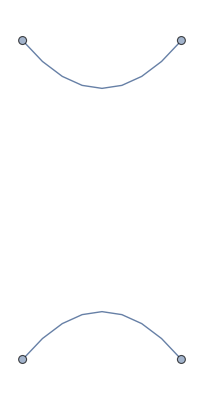
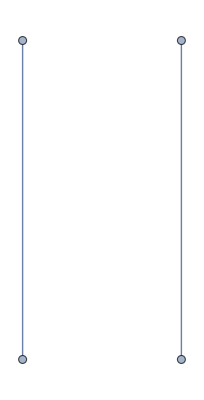
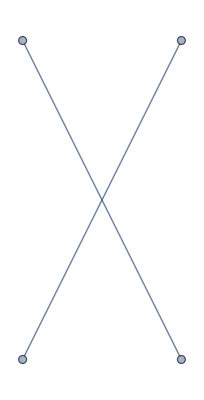
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

{g | i1 | i2
  |   g |   |  
i3 | i4,δ | i1 |  
  | i3 δ | i2 |  
  | i4,δ | i1 |  
  | i4 δ | i2 |  
  | i3}

```mathematica
BrauerElements[2]
BrauerDiagram/@%
BrauerToTensor/@%
```

```mathematica
Flatten@BrauerTableaux[4]
TableauForm/@%
BrauerToTensor/@%%
```

{{{1,2,3,3}}_Tab,{{1,3,2,3}}_Tab,{{1,2,3},{3}}_Tab,{{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab,{{1,2,1,2}}_Tab,{{1,2},{1,2}}_Tab}

{1 | 2 | 3 | 3,1 | 3 | 2 | 3,1 | 2 | 3
3 |  | ,1 | 2
3 | 3,1 | 2
3 | 
3 | ,1 | 2 | 1 | 2,1 | 2
1 | 2}

{δ | i2 |  
  | j4 δ | i4 |  
  | j3 g | i1 | i3
  |   g |   |  
j1 | j2+δ | i2 |  
  | j3 δ | i3 |  
  | j4 g | i1 | i4
  |   g |   |  
j1 | j2+δ | i1 |  
  | j4 δ | i4 |  
  | j3 g | i2 | i3
  |   g |   |  
j1 | j2+δ | i1 |  
  | j3 δ | i3 |  
  | j4 g | i2 | i4
  |   g |   |  
j1 | j2+δ | i3 |  
  | j4 δ | i4 |  
  | j2 g | i1 | i2
  |   g |   |  
j1 | j3+δ | i2 |  
  | j4 δ | i3 |  
  | j2 g | i1 | i4
  |   g |   |  
j1 | j3+δ | i1 |  
  | j4 δ | i4 |  
  | j2 g | i2 | i3
  |   g |   |  
j1 | j3+δ | i1 |  
  | j2 δ | i2 |  
  | j4 g | i3 | i4
  |   g |   |  
j1 | j3+δ | i3 |  
  | j2 δ | i4 |  
  | j3 g | i1 | i2
  |   g |   |  
j1 | j4+δ | i2 |  
  | j3 δ | i4 |  
  | j2 g | i1 | i3
  |   g |   |  
j1 | j4+δ | i1 |  
  | j3 δ | i3 |  
  | j2 g | i2 | i4
  |   g |   |  
j1 | j4+δ | i1 |  
  | j2 δ | i2 |  
  | j3 g | i3 | i4
  |   g |   |  
j1 | j4+δ | i3 |  
  | j4 δ | i4 |  
  | j1 g | i1 | i2
  |   g |   |  
j2 | j3+δ | i2 |  
  | j4 δ | i4 |  
  | j1 g | i1 | i3
  |   g |   |  
j2 | j3+δ | i1 |  
  | j4 δ | i3 |  
  | j1 g | i2 | i4
  |   g |   |  
j2 | j3+δ | i1 |  
  | j4 δ | i2 |  
  | j1 g | i3 | i4
  |   g |   |  
j2 | j3+δ | i3 |  
  | j1 δ | i4 |  
  | j3 g | i1 | i2
  |   g |   |  
j2 | j4+δ | i2 |  
  | j3 δ | i3 |  
  | j1 g | i1 | i4
  |   g |   |  
j2 | j4+δ | i1 |  
  | j3 δ | i4 |  
  | j1 g | i2 | i3
  |   g |   |  
j2 | j4+δ | i1 |  
  | j3 δ | i2 |  
  | j1 g | i3 | i4
  |   g |   |  
j2 | j4+δ | i2 |  
  | j1 δ | i4 |  
  | j2 g | i1 | i3
  |   g |   |  
j3 | j4+δ | i2 |  
  | j1 δ | i3 |  
  | j2 g | i1 | i4
  |   g |   |  
j3 | j4+δ | i1 |  
  | j2 δ | i4 |  
  | j1 g | i2 | i3
  |   g |   |  
j3 | j4+δ | i1 |  
  | j2 δ | i3 |  
  | j1 g | i2 | i4
  |   g |   |  
j3 | j4,δ | i1 |  
  | j4 δ | i2 |  
  | j3 g | i3 | i4
  |   g |   |  
j1 | j2+δ | i1 |  
  | j3 δ | i2 |  
  | j4 g | i3 | i4
  |   g |   |  
j1 | j2+δ | i1 |  
  | j4 δ | i3 |  
  | j2 g | i2 | i4
  |   g |   |  
j1 | j3+δ | i1 |  
  | j2 δ | i3 |  
  | j4 g | i2 | i4
  |   g |   |  
j1 | j3+δ | i1 |  
  | j3 δ | i4 |  
  | j2 g | i2 | i3
  |   g |   |  
j1 | j4+δ | i1 |  
  | j2 δ | i4 |  
  | j3 g | i2 | i3
  |   g |   |  
j1 | j4+δ | i2 |  
  | j4 δ | i3 |  
  | j1 g | i1 | i4
  |   g |   |  
j2 | j3+δ | i2 |  
  | j1 δ | i3 |  
  | j4 g | i1 | i4
  |   g |   |  
j2 | j3+δ | i2 |  
  | j3 δ | i4 |  
  | j1 g | i1 | i3
  |   g |   |  
j2 | j4+δ | i2 |  
  | j1 δ | i4 |  
  | j3 g | i1 | i3
  |   g |   |  
j2 | j4+δ | i3 |  
  | j2 δ | i4 |  
  | j1 g | i1 | i2
  |   g |   |  
j3 | j4+δ | i3 |  
  | j1 δ | i4 |  
  | j2 g | i1 | i2
  |   g |   |  
j3 | j4,δ | i2 |  
  | j3 δ | i4 |  
  | j4 g | i1 | i3
  |   g |   |  
j1 | j2+δ | i2 |  
  | j4 δ | i3 |  
  | j3 g | i1 | i4
  |   g |   |  
j1 | j2+δ | i1 |  
  | j3 δ | i4 |  
  | j4 g | i2 | i3
  |   g |   |  
j1 | j2+δ | i1 |  
  | j4 δ | i3 |  
  | j3 g | i2 | i4
  |   g |   |  
j1 | j2+δ | i3 |  
  | j2 δ | i4 |  
  | j4 g | i1 | i2
  |   g |   |  
j1 | j3+δ | i2 |  
  | j2 δ | i3 |  
  | j4 g | i1 | i4
  |   g |   |  
j1 | j3+δ | i1 |  
  | j2 δ | i4 |  
  | j4 g | i2 | i3
  |   g |   |  
j1 | j3+δ | i1 |  
  | j4 δ | i2 |  
  | j2 g | i3 | i4
  |   g |   |  
j1 | j3+δ | i3 |  
  | j3 δ | i4 |  
  | j2 g | i1 | i2
  |   g |   |  
j1 | j4+δ | i2 |  
  | j2 δ | i4 |  
  | j3 g | i1 | i3
  |   g |   |  
j1 | j4+δ | i1 |  
  | j2 δ | i3 |  
  | j3 g | i2 | i4
  |   g |   |  
j1 | j4+δ | i1 |  
  | j3 δ | i2 |  
  | j2 g | i3 | i4
  |   g |   |  
j1 | j4+δ | i3 |  
  | j1 δ | i4 |  
  | j4 g | i1 | i2
  |   g |   |  
j2 | j3+δ | i2 |  
  | j1 δ | i4 |  
  | j4 g | i1 | i3
  |   g |   |  
j2 | j3+δ | i1 |  
  | j1 δ | i3 |  
  | j4 g | i2 | i4
  |   g |   |  
j2 | j3+δ | i1 |  
  | j1 δ | i2 |  
  | j4 g | i3 | i4
  |   g |   |  
j2 | j3+δ | i3 |  
  | j3 δ | i4 |  
  | j1 g | i1 | i2
  |   g |   |  
j2 | j4+δ | i2 |  
  | j1 δ | i3 |  
  | j3 g | i1 | i4
  |   g |   |  
j2 | j4+δ | i1 |  
  | j1 δ | i4 |  
  | j3 g | i2 | i3
  |   g |   |  
j2 | j4+δ | i1 |  
  | j1 δ | i2 |  
  | j3 g | i3 | i4
  |   g |   |  
j2 | j4+δ | i2 |  
  | j2 δ | i4 |  
  | j1 g | i1 | i3
  |   g |   |  
j3 | j4+δ | i2 |  
  | j2 δ | i3 |  
  | j1 g | i1 | i4
  |   g |   |  
j3 | j4+δ | i1 |  
  | j1 δ | i4 |  
  | j2 g | i2 | i3
  |   g |   |  
j3 | j4+δ | i1 |  
  | j1 δ | i3 |  
  | j2 g | i2 | i4
  |   g |   |  
j3 | j4,δ | i3 |  
  | j4 δ | i4 |  
  | j3 g | i1 | i2
  |   g |   |  
j1 | j2+δ | i2 |  
  | j4 δ | i4 |  
  | j2 g | i1 | i3
  |   g |   |  
j1 | j3+δ | i2 |  
  | j3 δ | i3 |  
  | j2 g | i1 | i4
  |   g |   |  
j1 | j4+δ | i1 |  
  | j4 δ | i4 |  
  | j1 g | i2 | i3
  |   g |   |  
j2 | j3+δ | i1 |  
  | j3 δ | i3 |  
  | j1 g | i2 | i4
  |   g |   |  
j2 | j4+δ | i1 |  
  | j2 δ | i2 |  
  | j1 g | i3 | i4
  |   g |   |  
j3 | j4,δ | i3 |  
  | j3 δ | i4 |  
  | j4 g | i1 | i2
  |   g |   |  
j1 | j2+δ | i2 |  
  | j2 δ | i4 |  
  | j4 g | i1 | i3
  |   g |   |  
j1 | j3+δ | i2 |  
  | j2 δ | i3 |  
  | j3 g | i1 | i4
  |   g |   |  
j1 | j4+δ | i1 |  
  | j1 δ | i4 |  
  | j4 g | i2 | i3
  |   g |   |  
j2 | j3+δ | i1 |  
  | j1 δ | i3 |  
  | j3 g | i2 | i4
  |   g |   |  
j2 | j4+δ | i1 |  
  | j1 δ | i2 |  
  | j2 g | i3 | i4
  |   g |   |  
j3 | j4,g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
j1 | j4 g |   |  
j2 | j3+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
j1 | j4 g |   |  
j2 | j3+g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
j1 | j3 g |   |  
j2 | j4+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
j1 | j3 g |   |  
j2 | j4+g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
j1 | j2 g |   |  
j3 | j4+g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
j1 | j2 g |   |  
j3 | j4,g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
j1 | j4 g |   |  
j2 | j3+g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
j1 | j3 g |   |  
j2 | j4+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
j1 | j2 g |   |  
j3 | j4}

```mathematica
(*** Traceless projector ***)
```

```mathematica
TracelessProjector[3,1,g]
```

δ | i1 |  
  | i4 δ | i2 |  
  | j1 δ | i3 |  
  | j2+(δ | i2 |  
  | j2 g | i1 | i3
  |   g |   |  
i4 | j1+δ | i1 |  
  | j2 g | i2 | i3
  |   g |   |  
i4 | j1+δ | i3 |  
  | j1 g | i1 | i2
  |   g |   |  
i4 | j2+δ | i1 |  
  | j1 g | i2 | i3
  |   g |   |  
i4 | j2+δ | i3 |  
  | i4 g | i1 | i2
  |   g |   |  
j1 | j2+δ | i2 |  
  | i4 g | i1 | i3
  |   g |   |  
j1 | j2)/((-1+d) (2+d))-((1+d) (δ | i3 |  
  | j2 g | i1 | i2
  |   g |   |  
i4 | j1+δ | i2 |  
  | j1 g | i1 | i3
  |   g |   |  
i4 | j2+δ | i1 |  
  | i4 g | i2 | i3
  |   g |   |  
j1 | j2))/((-1+d) (2+d))

```mathematica
DefTensor[H[-i1,-i2,-i3],M]
```

** DefTensor: Defining tensor H[-i1,-i2,-i3].

```mathematica
TracelessProjector[3,1,g]*H[-i1,-i2,-i3]//ContractMetric
%*g[j1,j2]//ContractMetric//SameDummies//Simplify
%*g[j1,j3]//ContractMetric//SameDummies//Simplify
%*g[j2,j3]//ContractMetric//SameDummies//Simplify
```

(g |   |  
j1 | j2 H |   | i1 |  
i1 |   | i4)/((-1+d) (2+d))+(g |   |  
i4 | j2 H |   | i1 |  
i1 |   | j1)/((-1+d) (2+d))-(g |   |  
i4 | j1 H |   | i1 |  
i1 |   | j2)/((-1+d) (2+d))-(d g |   |  
i4 | j1 H |   | i1 |  
i1 |   | j2)/((-1+d) (2+d))+(g |   |  
j1 | j2 H |   |   | i1
i1 | i4 |)/((-1+d) (2+d))-(g |   |  
i4 | j2 H |   |   | i1
i1 | j1 |)/((-1+d) (2+d))-(d g |   |  
i4 | j2 H |   |   | i1
i1 | j1 |)/((-1+d) (2+d))+(g |   |  
i4 | j1 H |   |   | i1
i1 | j2 |)/((-1+d) (2+d))-(g |   |  
j1 | j2 H |   |   | i2
i4 | i2 |)/((-1+d) (2+d))-(d g |   |  
j1 | j2 H |   |   | i2
i4 | i2 |)/((-1+d) (2+d))+H |   |   |  
i4 | j1 | j2+(g |   |  
i4 | j2 H |   |   | i2
j1 | i2 |)/((-1+d) (2+d))+(g |   |  
i4 | j1 H |   |   | i2
j2 | i2 |)/((-1+d) (2+d))

0

0

0

```mathematica
(*** There is more about the trace decomposition of a tensor in the xMAG tutorial ... ***)
```

## VI. Others function related to the Symmetric group and Young tableaux

```mathematica
?StdTableaux
```

```mathematica
StdTableaux[4]
```

{{{1,2,3,4}},{{1,2,3},{4}},{{1,2,4},{3}},{{1,3,4},{2}},{{1,2},{3,4}},{{1,3},{2,4}},{{1,2},{3},{4}},{{1,3},{2},{4}},{{1,4},{2},{3}},{{1},{2},{3},{4}}}

```mathematica
?BratteliPath
```

```mathematica
StdTableaux[4]
BratteliPath/@%
```

{{{1,2,3,4}},{{1,2,3},{4}},{{1,2,4},{3}},{{1,3,4},{2}},{{1,2},{3,4}},{{1,3},{2,4}},{{1,2},{3},{4}},{{1,3},{2},{4}},{{1,4},{2},{3}},{{1},{2},{3},{4}}}

{{{{1}},{{1,2}},{{1,2,3}},{{1,2,3,4}}},{{{1}},{{1,2}},{{1,2,3}},{{1,2,3},{4}}},{{{1}},{{1,2}},{{1,2},{3}},{{1,2,4},{3}}},{{{1}},{{1},{2}},{{1,3},{2}},{{1,3,4},{2}}},{{{1}},{{1,2}},{{1,2},{3}},{{1,2},{3,4}}},{{{1}},{{1},{2}},{{1,3},{2}},{{1,3},{2,4}}},{{{1}},{{1,2}},{{1,2},{3}},{{1,2},{3},{4}}},{{{1}},{{1},{2}},{{1,3},{2}},{{1,3},{2},{4}}},{{{1}},{{1},{2}},{{1},{2},{3}},{{1,4},{2},{3}}},{{{1}},{{1},{2}},{{1},{2},{3}},{{1},{2},{3},{4}}}}

```mathematica
?YoungProjector
?SNYoungProjector
```

```mathematica
StdTableaux[3]
YoungProjector/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{1/6 (id+(1,2)+(1,3)+(2,3)+(1,2,3)+(1,3,2)),1/3 (id+(1,2)-(1,3)-(1,2,3)),1/3 (id-(1,2)+(1,3)-(1,3,2)),1/6 (id-(1,2)-(1,3)-(2,3)+(1,2,3)+(1,3,2))}

```mathematica
StdTableaux[3]
SNYoungProjector/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{1/6 (id+(1,2)+(1,3)+(2,3)+(1,2,3)+(1,3,2)),1/6 (2 id+2(1,2)-(1,3)-(2,3)-(1,2,3)-(1,3,2)),1/6 (2 id-2(1,2)+(1,3)+(2,3)-(1,2,3)-(1,3,2)),1/6 (id-(1,2)-(1,3)-(2,3)+(1,2,3)+(1,3,2))}